# Piece of Cake coordinates deduction

## Coordinate system description

The coordinates used here are based upon https://arxiv.org/abs/gr-qc/0512001v1 (sec. IV, equations (18)-(19) and unnumbered equations in-between)
Each patch will use local coordinates labeled (a,b,c) limited to the [-1,1] range and is embedded in a global Cartesian coordinate system with coordinates (x,y,z).  
In each patch, the c coordinate points outward in the radial direction.
In each patch, the coordinate system is right handed

## Patch system skeleton

```mathematica
ClearAll[F];
F[a_,b_,c_]=(((r1-r[c])+(r[c]-r0)Ee[a,b])/(r1-r0))^(1/2);

ClearAll[r];
r[c_]=1/2(r0(1-c)+r1(1+c));

ClearAll[Ee];
Ee[a_,b_]=1+a^2+b^2;

ClearAll[core];
core[a_,b_,c_]=FullSimplify[r[c]/F[a,b,c]];

ClearAll[CakePlusX];
CakePlusX={1,b,a}*core[a,b,c];

ClearAll[CakePlusY];
CakePlusY={-b,1,a}*core[a,b,c];

ClearAll[CakePlusZ];
CakePlusZ={-a,b,1}*core[a,b,c];

ClearAll[CakeMinusX];
CakeMinusX={-1,-b,a}*core[a,b,c];

ClearAll[CakeMinusY];
CakeMinusY={b,-1,a}*core[a,b,c];

ClearAll[CakeMinusZ];
CakeMinusZ={a,b,-1}*core[a,b,c];

ClearAll[CakeCore];
CakeCore={a,b,c}*r0;
```

## Inverse coordinate transformations

First, let’s find the inverse coordinate transformations.

```mathematica
ClearAll[InverseCakePlusX,InverseCakeMinusX];
InverseCakePlusX={a,b,c}//.FullSimplify[Solve[CakePlusX=={x,y,z},{a,b,c}],x≥0]
InverseCakeMinusX={a,b,c}//.FullSimplify[Solve[CakeMinusX=={x,y,z},{a,b,c}],x≤0]

ClearAll[InverseCakePlusY,InverseCakeMinusY];
InverseCakePlusY={a,b,c}//.FullSimplify[Solve[CakePlusY=={x,y,z},{a,b,c}],y≥0]
InverseCakeMinusY={a,b,c}//.FullSimplify[Solve[CakeMinusY=={x,y,z},{a,b,c}],y≤0]

ClearAll[InverseCakePlusZ,InverseCakeMinusZ];
InverseCakePlusZ={a,b,c}//.FullSimplify[Solve[CakePlusZ=={x,y,z},{a,b,c}],z≥0]
InverseCakeMinusZ={a,b,c}//.FullSimplify[Solve[CakeMinusZ=={x,y,z},{a,b,c}],z≤0]

ClearAll[InverseCakeCore]
InverseCakeCore={a,b,c}//.FullSimplify[Solve[CakeCore=={x,y,z},{a,b,c}]]
```

{{z/x,y/x,(r0^2-r1^2+y^2+z^2-√(4 r1^2 x^2+(y^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (2 x^2+y^2+z^2)))/(r0-r1)^2},{z/x,y/x,(r0^2-r1^2+y^2+z^2+√(4 r1^2 x^2+(y^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (2 x^2+y^2+z^2)))/(r0-r1)^2}}

{{-z/x,y/x,(r0^2-r1^2+y^2+z^2-√(4 r1^2 x^2+(y^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (2 x^2+y^2+z^2)))/(r0-r1)^2},{-z/x,y/x,(r0^2-r1^2+y^2+z^2+√(4 r1^2 x^2+(y^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (2 x^2+y^2+z^2)))/(r0-r1)^2}}

{{z/y,-x/y,(r0^2-r1^2+x^2+z^2-√(4 r1^2 y^2+(x^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (x^2+2 y^2+z^2)))/(r0-r1)^2},{z/y,-x/y,(r0^2-r1^2+x^2+z^2+√(4 r1^2 y^2+(x^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (x^2+2 y^2+z^2)))/(r0-r1)^2}}

{{-z/y,-x/y,(r0^2-r1^2+x^2+z^2-√(4 r1^2 y^2+(x^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (x^2+2 y^2+z^2)))/(r0-r1)^2},{-z/y,-x/y,(r0^2-r1^2+x^2+z^2+√(4 r1^2 y^2+(x^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (x^2+2 y^2+z^2)))/(r0-r1)^2}}

{{-x/z,y/z,(r0^2-r1^2+x^2+y^2-√((x^2+y^2) (4 r0 (r0-r1)+x^2+y^2)+4 (r0-r1)^2 z^2))/(r0-r1)^2},{-x/z,y/z,(r0^2-r1^2+x^2+y^2+√((x^2+y^2) (4 r0 (r0-r1)+x^2+y^2)+4 (r0-r1)^2 z^2))/(r0-r1)^2}}

{{-x/z,-y/z,(r0^2-r1^2+x^2+y^2-√((x^2+y^2) (4 r0 (r0-r1)+x^2+y^2)+4 (r0-r1)^2 z^2))/(r0-r1)^2},{-x/z,-y/z,(r0^2-r1^2+x^2+y^2+√((x^2+y^2) (4 r0 (r0-r1)+x^2+y^2)+4 (r0-r1)^2 z^2))/(r0-r1)^2}}

{{x/r0,y/r0,z/r0}}

Note that
1. Thanks to the quadratic nature of the inverse problem, the coordinate transformations are ambiguous in the c component and a choice of sign must be made.
2. A common function can be defined for the c coordinate transformation.

In order to choose a sign for the square root, let’s construct a function that computes the error in going from a local coordinate, to a global coordinate and back to the original local coordinate for each patch

```mathematica
ClearAll[mismatch];
mismatch[patch_,inversePatch_,inverseIdx_,R0_,R1_,A_,B_,C_]:=Module[
{local2global,global2local,diff},

local2global=patch//.{r0->R0,r1->R1,a->A,b->B,c->C};
global2local=inversePatch⟦inverseIdx⟧//.{r0->R0,r1->R1,x->local2global⟦1⟧,y->local2global⟦2⟧,z->local2global⟦3⟧};

diff=Abs[{A,B,C}-global2local];

Return[diff.diff];
];

ClearAll[mismatchPlot];
mismatchPlot[patch_,inversePatch_]:=Plot[
{
mismatch[patch,inversePatch,2,1,2,a,-1,-1],
mismatch[patch,inversePatch,1,1,2,a,-1,-1]},

{a,-1.5,1.5},

PlotRange->Full,

PlotLegends->{"Positive root","Negative root"},

PlotStyle->{Directive[Red,Thick],Directive[Black,Thick]},

Axes->False,
Frame->True,
FrameLabel->{"a","mismatch"},

ImageSize->Large
];
```

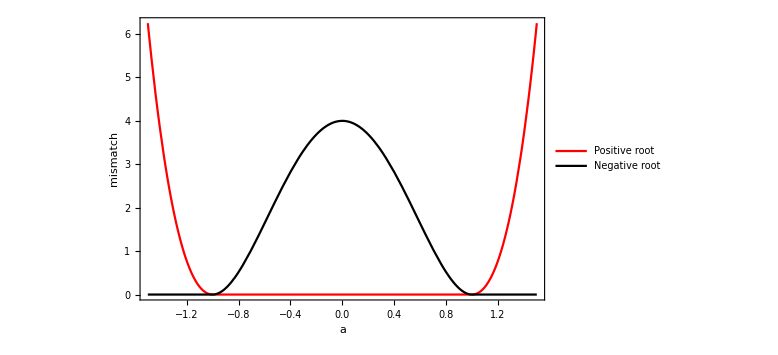

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
mismatchPlot[CakePlusX,InverseCakePlusX]
mismatchPlot[CakePlusY,InverseCakePlusY]
mismatchPlot[CakePlusZ,InverseCakePlusZ]
mismatchPlot[CakeMinusX,InverseCakeMinusX]
mismatchPlot[CakeMinusY,InverseCakeMinusY]
mismatchPlot[CakeMinusZ,InverseCakeMinusZ]
```

Note that outside of the [-1,1] range, the positive root solution gives incorrect results. On the other hand, the negative root solutions give correct results. We would like our inverse functions to cover a range that slighlty extends [-1,1] in order to cover the patch ghost zones. The point where positive root solutions start to become invalid is the location where the square root is zero. To better visualize the square root terms, we will write the transformations in terms of a,b,c and Ee

```mathematica
FullSimplify[FullSimplify[InverseCakePlusX//.Flatten[Solve[{InverseCakePlusX⟦1,1⟧==a,InverseCakePlusX⟦1,2⟧==b},{y,z}]]]//.{a^2->Eee-1-b^2}]
FullSimplify[FullSimplify[InverseCakeMinusX//.Flatten[Solve[{InverseCakeMinusX⟦1,1⟧==a,InverseCakeMinusX⟦1,2⟧==b},{y,z}]]]//.{a^2->Eee-1-b^2}]

FullSimplify[FullSimplify[InverseCakePlusY//.Flatten[Solve[{InverseCakePlusY⟦1,1⟧==a,InverseCakePlusY⟦1,2⟧==b},{x,z}]]]//.{a^2->Eee-1-b^2}]
FullSimplify[FullSimplify[InverseCakeMinusY//.Flatten[Solve[{InverseCakeMinusY⟦1,1⟧==a,InverseCakeMinusY⟦1,2⟧==b},{x,z}]]]//.{a^2->Eee-1-b^2}]

FullSimplify[FullSimplify[InverseCakePlusZ//.Flatten[Solve[{InverseCakePlusZ⟦1,1⟧==a,InverseCakePlusZ⟦1,2⟧==b},{x,y}]]]//.{a^2->Eee-1-b^2}]
FullSimplify[FullSimplify[InverseCakeMinusZ//.Flatten[Solve[{InverseCakeMinusZ⟦1,1⟧==a,InverseCakeMinusZ⟦1,2⟧==b},{x,y}]]]//.{a^2->Eee-1-b^2}]
```

{{a,b,(r0^2-r1^2+(-1+Eee) x^2-√(4 (r0-r1) (Eee r0-r1) x^2+(-1+Eee)^2 x^4))/(r0-r1)^2},{a,b,(r0^2-r1^2+(-1+Eee) x^2+√(4 (r0-r1) (Eee r0-r1) x^2+(-1+Eee)^2 x^4))/(r0-r1)^2}}

{{a,b,(r0^2-r1^2+(-1+Eee) x^2-√(4 (r0-r1) (Eee r0-r1) x^2+(-1+Eee)^2 x^4))/(r0-r1)^2},{a,b,(r0^2-r1^2+(-1+Eee) x^2+√(4 (r0-r1) (Eee r0-r1) x^2+(-1+Eee)^2 x^4))/(r0-r1)^2}}

{{a,b,(r0^2-r1^2+(-1+Eee) y^2-√(4 (r0-r1) (Eee r0-r1) y^2+(-1+Eee)^2 y^4))/(r0-r1)^2},{a,b,(r0^2-r1^2+(-1+Eee) y^2+√(4 (r0-r1) (Eee r0-r1) y^2+(-1+Eee)^2 y^4))/(r0-r1)^2}}

{{a,b,(r0^2-r1^2+(-1+Eee) y^2-√(4 (r0-r1) (Eee r0-r1) y^2+(-1+Eee)^2 y^4))/(r0-r1)^2},{a,b,(r0^2-r1^2+(-1+Eee) y^2+√(4 (r0-r1) (Eee r0-r1) y^2+(-1+Eee)^2 y^4))/(r0-r1)^2}}

{{a,b,(r0^2-r1^2+(-1+Eee) z^2-√(4 (r0-r1) (Eee r0-r1) z^2+(-1+Eee)^2 z^4))/(r0-r1)^2},{a,b,(r0^2-r1^2+(-1+Eee) z^2+√(4 (r0-r1) (Eee r0-r1) z^2+(-1+Eee)^2 z^4))/(r0-r1)^2}}

{{a,b,(r0^2-r1^2+(-1+Eee) z^2-√(4 (r0-r1) (Eee r0-r1) z^2+(-1+Eee)^2 z^4))/(r0-r1)^2},{a,b,(r0^2-r1^2+(-1+Eee) z^2+√(4 (r0-r1) (Eee r0-r1) z^2+(-1+Eee)^2 z^4))/(r0-r1)^2}}

We can then find the conditions in which this term becomes zero:

```mathematica
FullSimplify[Refine[Reduce[{4 (r0-r1) (Eee r0-r1) xyz^2+(-1+Eee)^2 xyz^4==0},Reals],{xyz∈Reals,r0∈Reals,r1∈Reals,Eee∈Reals,r0>0,r1>0,r0<r1,1≤Eee≤3,xyz≠0}]]
```

Eee>r1/r0&&(xyz==-(2 √(-(r0-r1) (Eee r0-r1)))/(-1+Eee)||xyz==(2 √(-(r0-r1) (Eee r0-r1)))/(-1+Eee))

In order for the square root to never be null, these conditions must always be violated. One easy way to ensure that is to make Eee≤r1/r0. Since 1≤Eee≤3, we need to make sure that r1≥3r0. For safety, we shall demand that r1>4r0 in the code. With that, we can see that the ambiguity problem goes away from the domain of interest

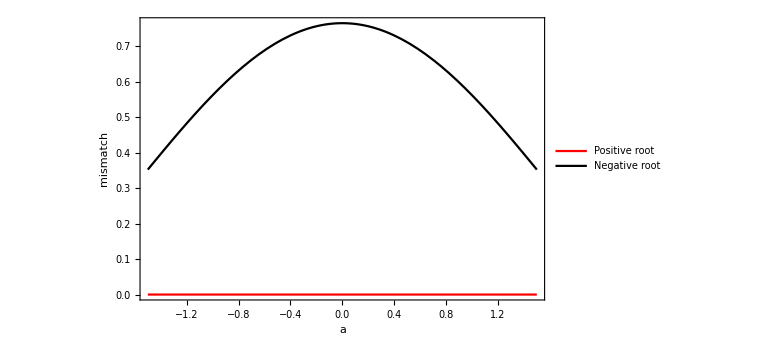

```mathematica
Plot[
{
mismatch[CakePlusX,InverseCakePlusX,2,1,5,a,-1,-1],
mismatch[CakePlusX,InverseCakePlusX,1,1,5,a,-1,-1]},

{a,-1.5,1.5},

PlotRange->Full,

PlotLegends->{"Positive root","Negative root"},

PlotStyle->{Directive[Red,Thick],Directive[Black,Thick]},

Axes->False,
Frame->True,
FrameLabel->{"a","mismatch"},

ImageSize->Large
]
```

## Final patch system

```mathematica
CakePlusX
CakeMinusX

CakePlusY
CakeMinusY

CakePlusZ
CakeMinusZ

CakeCore
```

{(r0-c r0+r1+c r1)/(√2 √(2+a^2 (1+c)+b^2 (1+c))),(b (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c))),(a (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c)))}

{-(r0-c r0+r1+c r1)/(√2 √(2+a^2 (1+c)+b^2 (1+c))),-(b (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c))),(a (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c)))}

{-(b (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c))),(r0-c r0+r1+c r1)/(√2 √(2+a^2 (1+c)+b^2 (1+c))),(a (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c)))}

{(b (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c))),-(r0-c r0+r1+c r1)/(√2 √(2+a^2 (1+c)+b^2 (1+c))),(a (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c)))}

{-(a (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c))),(b (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c))),(r0-c r0+r1+c r1)/(√2 √(2+a^2 (1+c)+b^2 (1+c)))}

{(a (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c))),(b (r0-c r0+r1+c r1))/(√2 √(2+a^2 (1+c)+b^2 (1+c))),-(r0-c r0+r1+c r1)/(√2 √(2+a^2 (1+c)+b^2 (1+c)))}

{a r0,b r0,c r0}

```mathematica
InverseCakePlusX=InverseCakePlusX⟦2⟧
InverseCakeMinusX=InverseCakeMinusX⟦2⟧

InverseCakePlusY=InverseCakePlusY⟦2⟧
InverseCakeMinusY=InverseCakeMinusY⟦2⟧

InverseCakePlusZ=InverseCakePlusZ⟦2⟧
InverseCakeMinusZ=InverseCakeMinusZ⟦2⟧

InverseCakeCore=InverseCakeCore⟦1⟧
```

{z/x,y/x,(r0^2-r1^2+y^2+z^2+√(4 r1^2 x^2+(y^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (2 x^2+y^2+z^2)))/(r0-r1)^2}

{-z/x,y/x,(r0^2-r1^2+y^2+z^2+√(4 r1^2 x^2+(y^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (2 x^2+y^2+z^2)))/(r0-r1)^2}

{z/y,-x/y,(r0^2-r1^2+x^2+z^2+√(4 r1^2 y^2+(x^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (x^2+2 y^2+z^2)))/(r0-r1)^2}

{-z/y,-x/y,(r0^2-r1^2+x^2+z^2+√(4 r1^2 y^2+(x^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (x^2+2 y^2+z^2)))/(r0-r1)^2}

{-x/z,y/z,(r0^2-r1^2+x^2+y^2+√((x^2+y^2) (4 r0 (r0-r1)+x^2+y^2)+4 (r0-r1)^2 z^2))/(r0-r1)^2}

{-x/z,-y/z,(r0^2-r1^2+x^2+y^2+√((x^2+y^2) (4 r0 (r0-r1)+x^2+y^2)+4 (r0-r1)^2 z^2))/(r0-r1)^2}

{x/r0,y/r0,z/r0}

```mathematica
DumpSave["cake_coord_transforms.mx",{
CakePlusX,
CakeMinusX,
CakePlusY,
CakeMinusY,
CakePlusZ,
CakeMinusZ,
CakeCore,
InverseCakePlusX,
InverseCakeMinusX,
InverseCakePlusY,
InverseCakeMinusY,
InverseCakePlusZ,
InverseCakeMinusZ,
InverseCakeCore
}];
```

## Transformations Code Generation

### Local2Global

```mathematica
Block[
{local2globalsrc,replace},
replace={"Power"->"pow","Sqrt"->"sqrt"};

local2globalsrc="CCTK_DEVICE CCTK_HOST svec local2global(const PatchTransformations &pt, int patch, const svec &local_vars) {
  using std::pow;
  using std::sqrt;

  const auto r0{pt.cake_inner_boundary_radius};
  const auto r1{pt.cake_outer_boundary_radius};

  const auto a{local_vars(0)};
  const auto b{local_vars(1)};
  const auto c{local_vars(2)};

  svec global_vars = {0.0, 0.0, 0.0};

  switch (patch) {\n\n"<>
  
"case static_cast<int>(patch_piece::cartesian):
    global_vars(0) = "<>StringReplace[ToString[CakeCore⟦1⟧,CForm],replace]<>";\n    "<>
"global_vars(1) = "<>StringReplace[ToString[CakeCore⟦2⟧,CForm],replace]<>";\n    "<>
"global_vars(2) = "<>StringReplace[ToString[CakeCore⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

  "case static_cast<int>(patch_piece::plus_x):
    global_vars(0) = "<>StringReplace[ToString[CakePlusX⟦1⟧,CForm],replace]<>";\n    "<>
"global_vars(1) = "<>StringReplace[ToString[CakePlusX⟦2⟧,CForm],replace]<>";\n    "<>
"global_vars(2) = "<>StringReplace[ToString[CakePlusX⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"case static_cast<int>(patch_piece::minus_x):
    global_vars(0) = "<>StringReplace[ToString[CakeMinusX⟦1⟧,CForm],replace]<>";\n    "<>
"global_vars(1) = "<>StringReplace[ToString[CakeMinusX⟦2⟧,CForm],replace]<>";\n    "<>
"global_vars(2) = "<>StringReplace[ToString[CakeMinusX⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"case static_cast<int>(patch_piece::plus_y):
    global_vars(0) = "<>StringReplace[ToString[CakePlusY⟦1⟧,CForm],replace]<>";\n    "<>
"global_vars(1) = "<>StringReplace[ToString[CakePlusY⟦2⟧,CForm],replace]<>";\n    "<>
"global_vars(2) = "<>StringReplace[ToString[CakePlusY⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"case static_cast<int>(patch_piece::minus_y):
    global_vars(0) = "<>StringReplace[ToString[CakeMinusY⟦1⟧,CForm],replace]<>";\n    "<>
"global_vars(1) = "<>StringReplace[ToString[CakeMinusY⟦2⟧,CForm],replace]<>";\n    "<>
"global_vars(2) = "<>StringReplace[ToString[CakeMinusY⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"case static_cast<int>(patch_piece::plus_z):
    global_vars(0) = "<>StringReplace[ToString[CakePlusZ⟦1⟧,CForm],replace]<>";\n    "<>
"global_vars(1) = "<>StringReplace[ToString[CakePlusZ⟦2⟧,CForm],replace]<>";\n    "<>
"global_vars(2) = "<>StringReplace[ToString[CakePlusZ⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"case static_cast<int>(patch_piece::minus_z):
    global_vars(0) = "<>StringReplace[ToString[CakeMinusZ⟦1⟧,CForm],replace]<>";\n    "<>
"global_vars(1) = "<>StringReplace[ToString[CakeMinusZ⟦2⟧,CForm],replace]<>";\n    "<>
"global_vars(2) = "<>StringReplace[ToString[CakeMinusZ⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"default:
#ifndef __CUDACC__
    CCTK_VERROR(\"No local -> global transformations available for patch %s\", piece_name(static_cast<patch_piece>(patch)).c_str());
#else
    assert(0);
#endif
    break;
  }
  
  return global_vars;
}";

Print[local2globalsrc]
]
```

CCTK_DEVICE CCTK_HOST svec local2global(const PatchTransformations &pt, int patch, const svec &local_vars) {
  using std::pow;
  using std::sqrt;

  const auto r0{pt.cake_inner_boundary_radius};
  const auto r1{pt.cake_outer_boundary_radius};

  const auto a{local_vars(0)};
  const auto b{local_vars(1)};
  const auto c{local_vars(2)};

  svec global_vars = {0.0, 0.0, 0.0};

  switch (patch) {

case static_cast<int>(patch_piece::cartesian):
    global_vars(0) = a*r0;
    global_vars(1) = b*r0;
    global_vars(2) = c*r0;
    break;

case static_cast<int>(patch_piece::plus_x):
    global_vars(0) = (r0 - c*r0 + r1 + c*r1)/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    global_vars(1) = (b*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    global_vars(2) = (a*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    break;

case static_cast<int>(patch_piece::minus_x):
    global_vars(0) = -((r0 - c*r0 + r1 + c*r1)/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c))));
    global_vars(1) = -((b*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c))));
    global_vars(2) = (a*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    break;

case static_cast<int>(patch_piece::plus_y):
    global_vars(0) = -((b*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c))));
    global_vars(1) = (r0 - c*r0 + r1 + c*r1)/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    global_vars(2) = (a*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    break;

case static_cast<int>(patch_piece::minus_y):
    global_vars(0) = (b*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    global_vars(1) = -((r0 - c*r0 + r1 + c*r1)/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c))));
    global_vars(2) = (a*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    break;

case static_cast<int>(patch_piece::plus_z):
    global_vars(0) = -((a*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c))));
    global_vars(1) = (b*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    global_vars(2) = (r0 - c*r0 + r1 + c*r1)/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    break;

case static_cast<int>(patch_piece::minus_z):
    global_vars(0) = (a*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    global_vars(1) = (b*(r0 - c*r0 + r1 + c*r1))/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c)));
    global_vars(2) = -((r0 - c*r0 + r1 + c*r1)/(sqrt(2)*sqrt(2 + pow(a,2)*(1 + c) + pow(b,2)*(1 + c))));
    break;

default:
#ifndef __CUDACC__
    CCTK_VERROR("No local -> global transformations available for patch %s", piece_name(static_cast<patch_piece>(patch)).c_str());
#else
    assert(0);
#endif
    break;
  }
  
  return global_vars;
}

### Global2Local

```mathematica
Block[
{local2globalsrc,replace},
replace={"Power"->"pow","Sqrt"->"sqrt"};

local2globalsrc="CCTK_DEVICE CCTK_HOST std_tuple<int, svec> global2local(const PatchTransformations &pt, const svec &global_vars) {
  using std::pow;
  using std::sqrt;

  const auto r0{pt.cake_inner_boundary_radius};
  const auto r1{pt.cake_outer_boundary_radius};

  const auto x{global_vars(0)};
  const auto y{global_vars(1)};
  const auto z{global_vars(2)};

  const auto piece{get_owner_patch(pt, global_vars)};

  svec local_vars{0.0, 0.0, 0.0};

  switch (static_cast<int>(piece)) {\n\n"<>

"case static_cast<int>(patch_piece::cartesian):
    local_vars(0) = "<>StringReplace[ToString[InverseCakeCore⟦1⟧,CForm],replace]<>";\n    "<>
"local_vars(1) = "<>StringReplace[ToString[InverseCakeCore⟦2⟧,CForm],replace]<>";\n    "<>
"local_vars(2) = "<>StringReplace[ToString[InverseCakeCore⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

  "case static_cast<int>(patch_piece::plus_x):
    local_vars(0) = "<>StringReplace[ToString[InverseCakePlusX⟦1⟧,CForm],replace]<>";\n    "<>
"local_vars(1) = "<>StringReplace[ToString[InverseCakePlusX⟦2⟧,CForm],replace]<>";\n    "<>
"local_vars(2) = "<>StringReplace[ToString[InverseCakePlusX⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"case static_cast<int>(patch_piece::minus_x):
    local_vars(0) = "<>StringReplace[ToString[InverseCakeMinusX⟦1⟧,CForm],replace]<>";\n    "<>
"local_vars(1) = "<>StringReplace[ToString[InverseCakeMinusX⟦2⟧,CForm],replace]<>";\n    "<>
"local_vars(2) = "<>StringReplace[ToString[InverseCakeMinusX⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"case static_cast<int>(patch_piece::plus_y):
    local_vars(0) = "<>StringReplace[ToString[InverseCakePlusY⟦1⟧,CForm],replace]<>";\n    "<>
"local_vars(1) = "<>StringReplace[ToString[InverseCakePlusY⟦2⟧,CForm],replace]<>";\n    "<>
"local_vars(2) = "<>StringReplace[ToString[InverseCakePlusY⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"case static_cast<int>(patch_piece::minus_y):
    local_vars(0) = "<>StringReplace[ToString[InverseCakeMinusY⟦1⟧,CForm],replace]<>";\n    "<>
"local_vars(1) = "<>StringReplace[ToString[InverseCakeMinusY⟦2⟧,CForm],replace]<>";\n    "<>
"local_vars(2) = "<>StringReplace[ToString[InverseCakeMinusY⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"case static_cast<int>(patch_piece::plus_z):
    local_vars(0) = "<>StringReplace[ToString[InverseCakePlusZ⟦1⟧,CForm],replace]<>";\n    "<>
"local_vars(1) = "<>StringReplace[ToString[InverseCakePlusZ⟦2⟧,CForm],replace]<>";\n    "<>
"local_vars(2) = "<>StringReplace[ToString[InverseCakePlusZ⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"case static_cast<int>(patch_piece::minus_z):
    local_vars(0) = "<>StringReplace[ToString[InverseCakeMinusZ⟦1⟧,CForm],replace]<>";\n    "<>
"local_vars(1) = "<>StringReplace[ToString[InverseCakeMinusZ⟦2⟧,CForm],replace]<>";\n    "<>
"local_vars(2) = "<>StringReplace[ToString[InverseCakeMinusZ⟦3⟧,CForm],replace]<>";\n    "<>
"break;\n\n"<>

"default:
#ifndef __CUDACC__
    CCTK_VERROR(\"At point (%f, %f, %f): No global -> local transformations available for patch %s.\", x, y, z, piece_name(piece).c_str());
#else
    assert(0);
#endif
    break;
  }
  
  return std_make_tuple(static_cast<int>(piece), local_vars);
}";

Print[local2globalsrc]
]
```

CCTK_DEVICE CCTK_HOST std_tuple<int, svec> global2local(const PatchTransformations &pt, const svec &global_vars) {
  using std::pow;
  using std::sqrt;

  const auto r0{pt.cake_inner_boundary_radius};
  const auto r1{pt.cake_outer_boundary_radius};

  const auto x{global_vars(0)};
  const auto y{global_vars(1)};
  const auto z{global_vars(2)};

  const auto piece{get_owner_patch(pt, global_vars)};

  svec local_vars{0.0, 0.0, 0.0};

  switch (static_cast<int>(piece)) {

case static_cast<int>(patch_piece::cartesian):
    local_vars(0) = x/r0;
    local_vars(1) = y/r0;
    local_vars(2) = z/r0;
    break;

case static_cast<int>(patch_piece::plus_x):
    local_vars(0) = z/x;
    local_vars(1) = y/x;
    local_vars(2) = (pow(r0,2) - pow(r1,2) + pow(y,2) + pow(z,2) + sqrt(4*pow(r1,2)*pow(x,2) + pow(pow(y,2) + pow(z,2),2) + 4*pow(r0,2)*(pow(x,2) + pow(y,2) + pow(z,2)) - 4*r0*r1*(2*pow(x,2) + pow(y,2) + pow(z,2))))/pow(r0 - r1,2);
    break;

case static_cast<int>(patch_piece::minus_x):
    local_vars(0) = -(z/x);
    local_vars(1) = y/x;
    local_vars(2) = (pow(r0,2) - pow(r1,2) + pow(y,2) + pow(z,2) + sqrt(4*pow(r1,2)*pow(x,2) + pow(pow(y,2) + pow(z,2),2) + 4*pow(r0,2)*(pow(x,2) + pow(y,2) + pow(z,2)) - 4*r0*r1*(2*pow(x,2) + pow(y,2) + pow(z,2))))/pow(r0 - r1,2);
    break;

case static_cast<int>(patch_piece::plus_y):
    local_vars(0) = z/y;
    local_vars(1) = -(x/y);
    local_vars(2) = (pow(r0,2) - pow(r1,2) + pow(x,2) + pow(z,2) + sqrt(4*pow(r1,2)*pow(y,2) + pow(pow(x,2) + pow(z,2),2) + 4*pow(r0,2)*(pow(x,2) + pow(y,2) + pow(z,2)) - 4*r0*r1*(pow(x,2) + 2*pow(y,2) + pow(z,2))))/pow(r0 - r1,2);
    break;

case static_cast<int>(patch_piece::minus_y):
    local_vars(0) = -(z/y);
    local_vars(1) = -(x/y);
    local_vars(2) = (pow(r0,2) - pow(r1,2) + pow(x,2) + pow(z,2) + sqrt(4*pow(r1,2)*pow(y,2) + pow(pow(x,2) + pow(z,2),2) + 4*pow(r0,2)*(pow(x,2) + pow(y,2) + pow(z,2)) - 4*r0*r1*(pow(x,2) + 2*pow(y,2) + pow(z,2))))/pow(r0 - r1,2);
    break;

case static_cast<int>(patch_piece::plus_z):
    local_vars(0) = -(x/z);
    local_vars(1) = y/z;
    local_vars(2) = (pow(r0,2) - pow(r1,2) + pow(x,2) + pow(y,2) + sqrt((pow(x,2) + pow(y,2))*(4*r0*(r0 - r1) + pow(x,2) + pow(y,2)) + 4*pow(r0 - r1,2)*pow(z,2)))/pow(r0 - r1,2);
    break;

case static_cast<int>(patch_piece::minus_z):
    local_vars(0) = -(x/z);
    local_vars(1) = -(y/z);
    local_vars(2) = (pow(r0,2) - pow(r1,2) + pow(x,2) + pow(y,2) + sqrt((pow(x,2) + pow(y,2))*(4*r0*(r0 - r1) + pow(x,2) + pow(y,2)) + 4*pow(r0 - r1,2)*pow(z,2)))/pow(r0 - r1,2);
    break;

default:
#ifndef __CUDACC__
    CCTK_VERROR("At point (%f, %f, %f): No global -> local transformations available for patch %s.", x, y, z, piece_name(piece).c_str());
#else
    assert(0);
#endif
    break;
  }
  
  return std_make_tuple(static_cast<int>(piece), local_vars);
}